```mathematica
(((3 ((3 ((3 x + 1)/2/2) + 1)/2/2) + 1)/2 /2/2 // Unevaluated ) /.  {3 -> a, 2 -> b} // Expand) /. {b -> "2", a -> "3"}
```

1/2^3+3/2^5+3^2/2^7+(3^3 x)/2^7

```mathematica
f[x_]:=((Unevaluated[x]/.  {3->a,2->b}//Expand)/.{b->"2",a->"3"})
```

```mathematica
f[(3((3((3x+1)/2/2)+1)/2/2)+1)/2 /2/2]
```

1/2^3+3/2^5+3^2/2^7+(3^3 x)/2^7

```mathematica
SetAttributes[f,HoldAll]
```

```mathematica
Collatz[a0_Integer,maxits_:1000]:=NestWhileList[If[EvenQ[#],#/2,3#+1]&,a0,Unequal[#,1,-1,-10,-34]&,1,maxits]
```

```mathematica
Collatz[3]
```

{3,10,5,16,8,4,2,1}

```mathematica
If[Mod[#,2]==0,2,3]&/@{13,40,20,10,5,16,8,4,2,1}
```

{3,2,2,2,3,2,2,2,2,3}

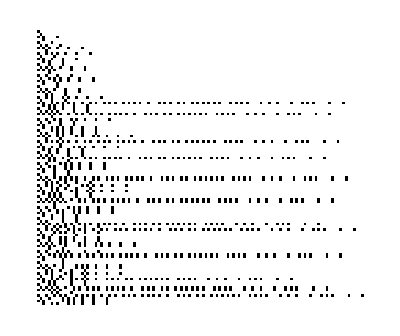

```mathematica
Table[If[Mod[#,2]==0,0,1]&/@Collatz[n],{n,1,100}]//ArrayPlot
```

```mathematica
Fold[If[EvenQ[#2],Defer[#1/2],Defer[3#1+1 ]]&,x,{3,2,2,2,2,2,2,3}]
```

```mathematica
3 (1/2 (1/2 (1/2 (1/2 (1/2 (1/2 (3 x+1)))))))+1//f
```

1+3/2^6+(3^2 x)/2^6

```mathematica
(Fold[If[EvenQ[#2],#1/a ,b#1+1 ]&,x,{3,2,2,2,2,2,2,3}]//Expand)/.{a->"2",b->"3"}
```

1+3/2^6+(3^2 x)/2^6

```mathematica
Table[(Fold[If[EvenQ[#2],#1/a ,b#1+1 ]&,x,#]//Expand)/.{a->"2",b->"3"}&@Collatz[n],{n,1,10}]//Column
```

1+3 x
1+(3 x)/2
1+3/2^4+3^2/2^5+(3^3 x)/2^5
1+(3 x)/2^2
1+3/2^4+(3^2 x)/2^4
1+3/2^4+3^2/2^5+(3^3 x)/2^6
1+3/2^4+3^2/2^7+3^3/2^9+3^4/2^10+3^5/2^11+(3^6 x)/2^11
1+(3 x)/2^3
1+3/2^4+3^2/2^7+3^3/2^9+3^4/2^10+3^5/2^11+3^6/2^13+(3^7 x)/2^13
1+3/2^4+(3^2 x)/2^5

```mathematica
Split/@ Table[If[Mod[#,2]==0,2,3]&/@Collatz[n],{n,1,10}]//Column
```

{{3}}
{{2},{3}}
{{3},{2},{3},{2,2,2,2},{3}}
{{2,2},{3}}
{{3},{2,2,2,2},{3}}
{{2},{3},{2},{3},{2,2,2,2},{3}}
{{3},{2},{3},{2},{3},{2,2},{3},{2,2,2},{3},{2,2,2,2},{3}}
{{2,2,2},{3}}
{{3},{2,2},{3},{2},{3},{2},{3},{2,2},{3},{2,2,2},{3},{2,2,2,2},{3}}
{{2},{3},{2,2,2,2},{3}}

```mathematica
Table[If[Mod[#,2]==0,2,3]&/@Collatz[n],{n,1,10}]//Column
```

{3}
{2,3}
{3,2,3,2,2,2,2,3}
{2,2,3}
{3,2,2,2,2,3}
{2,3,2,3,2,2,2,2,3}
{3,2,3,2,3,2,2,3,2,2,2,3,2,2,2,2,3}
{2,2,2,3}
{3,2,2,3,2,3,2,3,2,2,3,2,2,2,3,2,2,2,2,3}
{2,3,2,2,2,2,3}

```mathematica
Map[Length,(Split/@ Table[If[Mod[#,2]==0,2,3]&/@Collatz[n],{n,1,100}]/.{3}->Nothing),{2}]//Column
```

{}
{1}
{1,4}
{2}
{4}
{1,1,4}
{1,1,2,3,4}
{3}
{2,1,1,2,3,4}
{1,4}
{1,2,3,4}
{2,1,4}
{3,4}
{1,1,1,2,3,4}
{1,1,1,5,4}
{4}
{2,3,4}
{1,2,1,1,2,3,4}
{1,3,1,2,3,4}
{2,4}
{6}
{1,1,2,3,4}
{1,1,5,4}
{3,1,4}
{2,1,3,1,2,3,4}
{1,3,4}
{1,2,1,1,1,1,2,2,1,2,1,1,2,1,1,1,2,3,1,1,2,1,2,1,1,1,1,1,3,1,1,1,4,2,2,4,3,1,1,5,4}
{2,1,1,2,3,4}
{3,1,2,3,4}
{1,1,1,1,5,4}
{1,1,1,1,2,2,1,2,1,1,2,1,1,1,2,3,1,1,2,1,2,1,1,1,1,1,3,1,1,1,4,2,2,4,3,1,1,5,4}
{5}
{2,2,1,3,1,2,3,4}
{1,2,3,4}
{1,5,4}
{2,2,1,1,2,3,4}
{4,1,1,2,3,4}
{1,1,3,1,2,3,4}
{1,1,2,1,4,1,3,1,2,3,4}
{3,4}
{2,1,1,1,1,2,2,1,2,1,1,2,1,1,1,2,3,1,1,2,1,2,1,1,1,1,1,3,1,1,1,4,2,2,4,3,1,1,5,4}
{1,6}
{1,2,2,4,1,1,2,3,4}
{2,1,2,3,4}
{3,2,3,4}
{1,1,1,5,4}
{1,1,1,2,2,1,2,1,1,2,1,1,1,2,3,1,1,2,1,2,1,1,1,1,1,3,1,1,1,4,2,2,4,3,1,1,5,4}
{4,1,4}
{2,4,1,1,2,3,4}
{1,2,1,3,1,2,3,4}
{1,3,3,1,2,3,4}
{2,3,4}
{5,4}
{1,1,2,1,1,1,1,2,2,1,2,1,1,2,1,1,1,2,3,1,1,2,1,2,1,1,1,1,1,3,1,1,1,4,2,2,4,3,1,1,5,4}
{1,1,3,1,1,1,2,2,1,2,1,1,2,1,1,1,2,3,1,1,2,1,2,1,1,1,1,1,3,1,1,1,4,2,2,4,3,1,1,5,4}
{3,1,1,2,3,4}
{2,1,2,2,4,1,1,2,3,4}
{1,3,1,2,3,4}
{1,2,1,4,1,3,1,2,3,4}
{2,1,1,1,5,4}
{3,1,1,5,4}
{1,1,1,1,1,2,2,1,2,1,1,2,1,1,1,2,3,1,1,2,1,2,1,1,1,1,1,3,1,1,1,4,2,2,4,3,1,1,5,4}
{1,1,1,1,1,4,1,2,1,1,2,1,1,1,2,3,1,1,2,1,2,1,1,1,1,1,3,1,1,1,4,2,2,4,3,1,1,5,4}
{6}
{2,2,4,1,1,2,3,4}
{1,2,2,1,3,1,2,3,4}
{1,4,1,3,1,2,3,4}
{2,2,3,4}
{4,3,4}
{1,1,5,4}
{1,1,2,2,1,2,1,1,2,1,1,1,2,3,1,1,2,1,2,1,1,1,1,1,3,1,1,1,4,2,2,4,3,1,1,5,4}
{3,2,1,1,2,3,4}
{2,1,1,3,1,1,1,2,2,1,2,1,1,2,1,1,1,2,3,1,1,2,1,2,1,1,1,1,1,3,1,1,1,4,2,2,4,3,1,1,5,4}
{1,4,1,1,2,3,4}
{1,2,8}
{2,1,3,1,2,3,4}
{3,3,1,2,3,4}
{1,1,1,2,1,4,1,3,1,2,3,4}
{1,1,1,3,4,1,3,1,2,3,4}
{4,4}
{2,3,1,1,5,4}
{1,2,1,1,1,1,2,2,1,2,1,1,2,1,1,1,2,3,1,1,2,1,2,1,1,1,1,1,3,1,1,1,4,2,2,4,3,1,1,5,4}
{1,3,1,1,1,2,2,1,2,1,1,2,1,1,1,2,3,1,1,2,1,2,1,1,1,1,1,3,1,1,1,4,2,2,4,3,1,1,5,4}
{2,6}
{8}
{1,1,2,2,4,1,1,2,3,4}
{1,1,4,4,1,1,2,3,4}
{3,1,2,3,4}
{2,1,4,1,3,1,2,3,4}
{1,3,2,3,4}
{1,2,1,1,2,1,1,1,2,3,1,1,2,1,2,1,1,1,1,1,3,1,1,1,4,2,2,4,3,1,1,5,4}
{2,1,1,5,4}
{3,1,5,4}
{1,1,1,1,2,2,1,2,1,1,2,1,1,1,2,3,1,1,2,1,2,1,1,1,1,1,3,1,1,1,4,2,2,4,3,1,1,5,4}
{1,1,1,1,4,1,2,1,1,2,1,1,1,2,3,1,1,2,1,2,1,1,1,1,1,3,1,1,1,4,2,2,4,3,1,1,5,4}
{5,1,4}
{2,2,1,1,3,1,1,1,2,2,1,2,1,1,2,1,1,1,2,3,1,1,2,1,2,1,1,1,1,1,3,1,1,1,4,2,2,4,3,1,1,5,4}
{1,2,4,1,1,2,3,4}
{1,6,1,1,2,3,4}
{2,2,1,3,1,2,3,4}

### بحث جديد